```mathematica
dataSet = {{88.0,57.9},{224.7,108.2},{365.3,149.6},{687.0,228.07},{4332,778.434},{10760,1428.74},{30684,2839.08},{60188,4490.8},{90467,5879.13}};
```

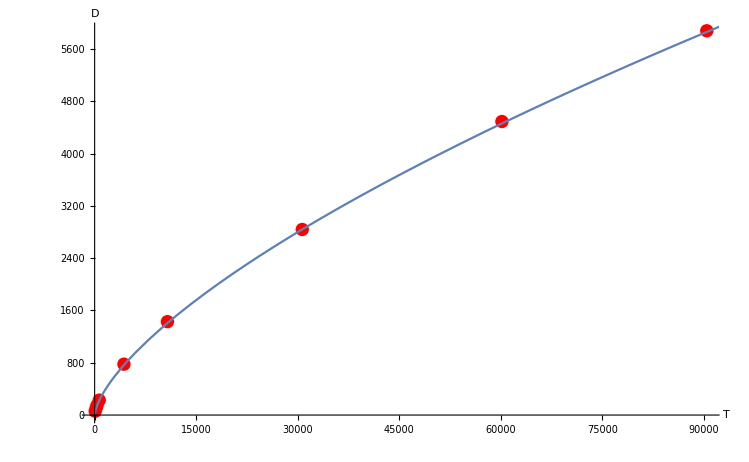

```mathematica
Show[
ListPlot[dataSet,AxesLabel->{T ,D}, PlotStyle->Red],
Plot[Function[x,2.8x^(0.67)][x],{x,0,100000}],
Legended-> {"A","B"}
]
```